```mathematica
rawData={{280,770},{284,800},{292,840},{295,810},{298,735},{305,640},{308,590},{315,560}};
```

-26219.1+189.205 x-0.331194 x^2

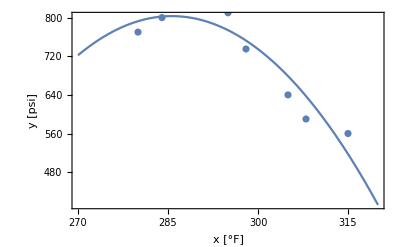

```mathematica
data=rawData;
y=Transpose[data][[2]];
X=Transpose[Table[Function[x,x^k]/@Transpose[data][[1]],{k,0,2}]];
model=NonlinearModelFit[data,Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2,{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2]},x];
model["BestFit"]
Show[Plot[model["BestFit"],{x,270,320},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"x [°F]","y [psi]"}],ListPlot[data]]
```

```mathematica
n=Length[data];p=2;
Syy=∑_(i=1)^n y[[i]]^2-1/n(∑_(i=1)^n y[[i]])^2;
SSR=Values[model["BestFitParameters"]].Transpose[X].y-1/n(∑_(i=1)^n y[[i]])^2;
SSE=Syy-SSR;
R2=model["RSquared"];
f=(n-p-1)/p*R2/(1-R2)
InverseCDF[FRatioDistribution[p,n-p-1],0.95]
```

1027.1

5.78614

```mathematica
model["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
b_0 | -26219.1 | 11910.7 | -2.20131 | 0.0789634
b_1 | 189.205 | 80.2397 | 2.35799 | 0.0649128
b_2 | -0.331194 | 0.134992 | -2.45343 | 0.0576924

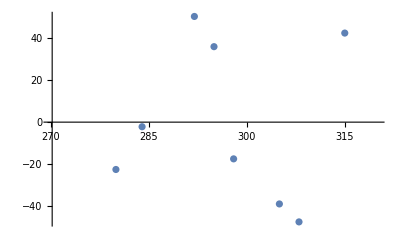

```mathematica
residuals=model["FitResiduals"];
ListPlot[Table[{data[[i]][[1]],residuals[[i]]},{i,1,n}],PlotRange->{{270,320},Automatic}]
```

```mathematica
model["ParameterConfidenceIntervalTable",ConfidenceLevel->0.975]
```

| Estimate | Standard Error | Confidence Interval
b_0 | -26219.1 | 11910.7 | {-63897.2,11458.9}
b_1 | 189.205 | 80.2397 | {-64.6244,443.033}
b_2 | -0.331194 | 0.134992 | {-0.758225,0.0958373}

```mathematica
model["SinglePredictionBands",ConfidenceLevel->0.975]/.{x->285}
```

{641.365,964.52}

759.395-90.7825 x-47.1655 x^2

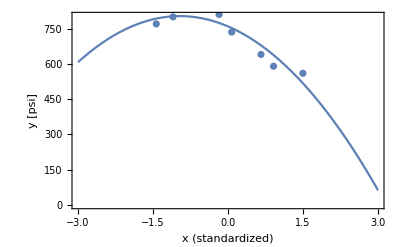

```mathematica
data=rawData;
data[[All,1]]=Standardize[data[[All,1]]];
y=Transpose[data][[2]];
X=Transpose[Table[Function[x,x^k]/@Transpose[data][[1]],{k,0,2}]];
model=NonlinearModelFit[data,Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2,{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2]},x];
model["BestFit"]
Show[Plot[model["BestFit"],{x,-3,3},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"x (standardized)","y [psi]"}],ListPlot[data]]
```

```mathematica
model["ParameterConfidenceIntervalTable",ConfidenceLevel->0.975]
```

| Estimate | Standard Error | Confidence Interval
b_0 | 759.395 | 23.2009 | {686.002,832.788}
b_1 | -90.7825 | 17.0824 | {-144.821,-36.7442}
b_2 | -47.1655 | 19.2243 | {-107.979,13.6483}

```mathematica
model["SinglePredictionBands",ConfidenceLevel->0.975]/.{x->(285-Mean[rawData[[All,1]]])/Sqrt[Variance[rawData[[All,1]]]]}
```

{641.365,964.52}

```mathematica
SSE
R2
Syy=∑_(i=1)^n y[[i]]^2-1/n(∑_(i=1)^n y[[i]])^2;
SSR=Values[model["BestFitParameters"]].Transpose[X].y-1/n(∑_(i=1)^n y[[i]])^2;
SSE=Syy-SSR
R2=model["RSquared"]
```

10213.

0.997572

10213.

0.997572

0.384851-0.846568 x-0.439829 x^2

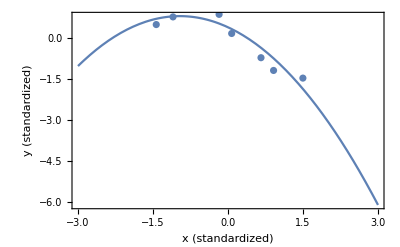

0.888124

0.873125

```mathematica
data=rawData;
data[[All,1]]=Standardize[data[[All,1]]];
data[[All,2]]=Standardize[data[[All,2]]];
y=Transpose[data][[2]];
X=Transpose[Table[Function[x,x^k]/@Transpose[data][[1]],{k,0,2}]];
model=NonlinearModelFit[data,Subscript[b, 0]+Subscript[b, 1] x+Subscript[b, 2] x^2,{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2]},x];
model["BestFit"]
Show[Plot[model["BestFit"],{x,-3,3},Frame->{True,True,False,False},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"x (standardized)","y (standardized)"}],ListPlot[data]]
Syy=∑_(i=1)^n y[[i]]^2-1/n(∑_(i=1)^n y[[i]])^2;
SSR=Values[model["BestFitParameters"]].Transpose[X].y-1/n(∑_(i=1)^n y[[i]])^2;
SSE=Syy-SSR
R2=model["RSquared"]
```